```mathematica
(*Code to calculate semi-automatically the NLO Higgs-strahlung cross section in the real triplet model*)
(*Authors:
      Main authors: Cristian Sierra, cristian.sierra@cern.ch
                    Qin Yu,
       Contributors: Mohamed Sassi,
                     Anjan Barik,
                     Manuel Diaz*)
(*Date: 04-07-2025*)
```

### Load FeynCalc

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/cristiansierra/Documents/GitHub/HiggsNLO/Models/Real_triplet/Calculator

```mathematica
Global`$LoadAddOns={"FeynHelpers"};
$LoadFeynArts=True;
<<FeynCalc`
$FAVerbose=0;
$CKM=True;
```

FeynCalc 10.0.0 (dev version). For help, use the online documentation, check out the wiki or visit the forum.

Please check our FAQ for answers to some common FeynCalc questions and have a look at the supplied examples.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynHelpers 2.0.0 (), for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please evaluate FeynHelpersHowToCite[] to learn how to correctly cite this work.

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

```mathematica
FAPatch[PatchModelsOnly->True]
```

Successfully patched FeynArts.

## Self-energies

### H

```mathematica
TopoΣ=CreateTopologies[1,1->1,ExcludeTopologies->{AllBoxes,Triangles}];
```

```mathematica
ΣHHDiag=InsertFields[TopoΣ,{S[1]}->{S[1]},Model->{"tripletSM"},
GenericModel->{"tripletSM"},InsertionLevel->{Particles},
ExcludeParticles->{S[1],V[1|2|3|4],U[1|2|3|4|11|12|31|32],F[_,{_}]}];
```

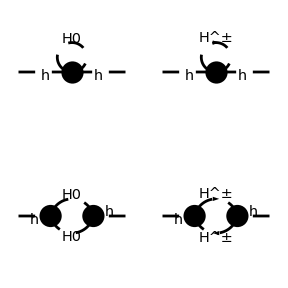

```mathematica
Paint[ΣHHDiag,ColumnsXRows->{2,2},Numbering->None];
```

```mathematica
ΣHHAmp[0]=FCFAConvert[CreateFeynAmp[ΣHHDiag,PreFactor->1,Truncated->True],
IncomingMomenta->{k},OutgoingMomenta->{k},TransversePolarizationVectors->{k},
Contract->True,LoopMomenta->{q},ChangeDimension->D,
UndoChiralSplittings->True,List->False,DropSumOver->False,
LorentzIndexNames->{µ,ν},FinalSubstitutions->{lam3->λ3,MH0->MH,MHch->MH}]/.FCGV[x_String]:>ToExpression[x]//
DiracSimplify[#,DiracSubstitute67->True]&//FCGVToSymbol//DiracSimplify;
```

```mathematica
(*When setting to True the following command rewrites A0 in terms of B0*)
```

```mathematica
SetOptions[A0,A0ToB0->False];
```

```mathematica
(*Tensor decomposition into Passarino Veltman functions:*)
```

```mathematica
ΣHHAmp[1]=  TID[ΣHHAmp[0],q,UsePaVeBasis->True,ToPaVe->True]//DiracSimplify;
```

```mathematica
ΣHH[0]=(-I)/(2 Pi)^4PaVeLimitTo4[ΣHHAmp[1]];
```

```mathematica
ΣHH[0]//FullSimplify//TraditionalForm
```

(3 λ3 (λ3 v^2 B_0((k̄)^2,MH^2,MH^2)+A_0(MH^2)))/(32 π^2)

#### Renormalization in MSbar scheme

```mathematica
ΣHH[1]=ΣHH[0]/.Pair[ Momentum[k], Momentum[k]]->kSquare;
```

```mathematica
ΣHHat[0]=FCHideEpsilon[PaXEvaluate[ΣHH[1],PaXAnalytic->True]];
```

```mathematica
ΣHHat[1]=ΣHHat[0]-SMP["Delta"]*Coefficient[ΣHHat[0],SMP["Delta"]];
```

```mathematica
(* Derivative of  *)
```

```mathematica
DΣHHat[0]=D[ΣHHat[1],kSquare];
```

```mathematica
(*  at  *)
```

```mathematica
DΣHHatFormh2=DΣHHat[0]/.kSquare->mh^2;
```

```mathematica
%//FullSimplify//TraditionalForm
```

(3 λ3^2 v^2 ((2 MH^2 log((-mh^2+√(mh^4-4 mh^2 MH^2)+2 MH^2)/(2 MH^2)))/(√(mh^4-4 mh^2 MH^2))-1))/(32 π^2 mh^2)

```mathematica
ΣHHatFors=ΣHHat[1]/.kSquare->s;
```

```mathematica
%//FullSimplify//TraditionalForm
```

(3 λ3 (s (log(μ^2/MH^2) (MH^2+λ3 v^2)-(MH^2 (-1+log(4)+2 log(π)))-2 λ3 v^2 (-1+log(2)+log(π)))+λ3 v^2 √(s (s-4 MH^2)) log((√(s (s-4 MH^2))+2 MH^2-s)/(2 MH^2))))/(32 π^2 s)

### ZZ

```mathematica
ΣZZDiag=InsertFields[TopoΣ,{V[2]}->{V[2]},Model->{"tripletSM"},GenericModel->{"tripletSM"},InsertionLevel->{Particles},ExcludeParticles->{S[Except[6]],V[1|3|4],U[1|2|3|4|11|12|31|32],F[_,{_}]}];
```

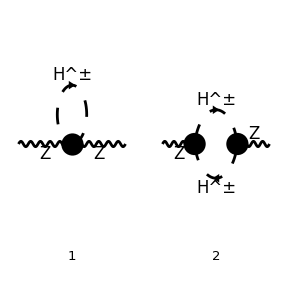

```mathematica
Paint[ΣZZDiag,ColumnsXRows->{2,1},Numbering->Simple];
```

```mathematica
ΣZZAmp[0]=DiracSimplify[FCFAConvert[CreateFeynAmp[ΣZZDiag,PreFactor->1,Truncated->True],IncomingMomenta->{k},OutgoingMomenta->{k},TransversePolarizationVectors->{k},Contract->True,LoopMomenta->{q},ChangeDimension->D,UndoChiralSplittings->True,List->False,DropSumOver->False,LorentzIndexNames->{µ,ν},FinalSubstitutions->{MH0->MH,MHch->MH}]/.FCGV[x_String]:>ToExpression[x],DiracSubstitute67->True]/.gc38->(FCGV["CW"]*FCGV["EL"])/FCGV["SW"]//DiracSimplify//FCGVToSymbol;
```

```mathematica
(*Tensor decomposition into Passarino Veltman functions:*)
```

```mathematica
ΣZZAmp[1]= TID[ΣZZAmp[0],q,UsePaVeBasis->True,ToPaVe->True]//DiracSimplify;
```

```mathematica
SetOptions[A0,A0ToB0->True];
```

```mathematica
ΣZZ=(-I)/(2 Pi)^4PaVeLimitTo4[ΣZZAmp[1]]//ChangeDimension[#,4]&;
```

```mathematica
(*Projecting out the transverse part, definition from hep-ph/0612057 Eq.50 ΣZZ= (-gµν+kµkν/k^2)ΣZZT + (kµkν/k^2) ΣZZL*)
```

```mathematica
TransverseProjector=(1/3)(-Pair[LorentzIndex[ν],LorentzIndex[µ]]+(Pair[LorentzIndex[ν],Momentum[k]] Pair[LorentzIndex[µ],Momentum[k]]/Pair[Momentum[k],Momentum[k]]));
ΣZZT[0]=Contract[TransverseProjector*ΣZZ];
ΣZZT[0]//Simplify//TraditionalForm
```

(CW^2 EL^2 (12 MH^2 (B_0(0,MH^2,MH^2)-B_0((k̄)^2,MH^2,MH^2))+(k̄)^2 (3 B_0((k̄)^2,MH^2,MH^2)+2)))/(144 π^2 SW^2)

#### Renormalization in MSbar scheme

```mathematica
ΣZZT[1]=ΣZZT[0]/.Pair[ Momentum[k], Momentum[k]]->kSquare;
```

```mathematica
ΣZZTHat[0]=FCHideEpsilon[PaXEvaluate[ΣZZT[1],PaXAnalytic->True]];
```

```mathematica
(* MS bar scheme *)
```

```mathematica
ΣZZTHat[1]=ΣZZTHat[0]-SMP["Delta"]*Coefficient[ΣZZTHat[0],SMP["Delta"]];
```

```mathematica
(*  at  and s *)
```

```mathematica
ΣZZTHatForMZ2=ΣZZTHat[1]/.kSquare->MZ^2;
```

```mathematica
ΣZZTHatFors=ΣZZTHat[1]/.kSquare->s;
```

```mathematica
(* Derivative of  *)
```

```mathematica
DΣZZTHat[0]=D[ΣZZTHat[1],kSquare];
```

```mathematica
(*  at  *)
```

```mathematica
DΣZZTHatforMZ2=DΣZZTHat[0]/.kSquare->MZ^2;
```

```mathematica
%//FullSimplify//TraditionalForm
```

(CW^2 EL^2 (3 MZ^4 log(μ^2/MH^2)+12 MH^2 MZ^2+3 (2 MH^2+MZ^2) √(MZ^4-4 MH^2 MZ^2) log((√(MZ^4-4 MH^2 MZ^2)+2 MH^2-MZ^2)/(2 MH^2))-MZ^4 (-5+log(64)+6 log(π))))/(144 π^2 MZ^4 SW^2)

### γZ

```mathematica
ΣγZDiag=InsertFields[TopoΣ,{V[1]}->{V[2]},Model->{"tripletSM"},GenericModel->{"tripletSM"},InsertionLevel->{Particles},ExcludeParticles->{S[Except[6]],V[1|3|4],U[1|2|3|4|11|12|31|32],F[_,{_}]}];
```

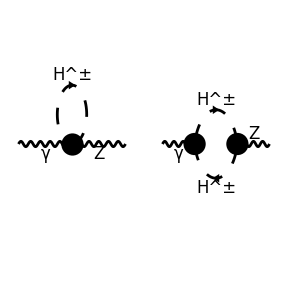

```mathematica
Paint[ΣγZDiag,ColumnsXRows->{2,1},Numbering->None];
```

```mathematica
ΣγZAmp[0]=DiracSimplify[FCFAConvert[CreateFeynAmp[ΣγZDiag,PreFactor->1,Truncated->True],IncomingMomenta->{k},OutgoingMomenta->{k},TransversePolarizationVectors->{k},Contract->True,LoopMomenta->{q},ChangeDimension->D,UndoChiralSplittings->True,List->False,DropSumOver->False,LorentzIndexNames->{µ,ν},FinalSubstitutions->{MH0->MH,MHch->MH}]/.FCGV[x_String]:>ToExpression[x],DiracSubstitute67->True]/.gc11->FCGV["EL"]/.gc38->(FCGV["CW"]*FCGV["EL"])/FCGV["SW"]//DiracSimplify//FCGVToSymbol;
```

```mathematica
(*Tensor decomposition into Passarino Veltman functions:*)
```

```mathematica
ΣγZAmp[1]= TID[ΣγZAmp[0],q,UsePaVeBasis->True,ToPaVe->True]//DiracSimplify;
```

```mathematica
ΣγZ=(-I)/(2 Pi)^4PaVeLimitTo4[ΣγZAmp[1]];
```

```mathematica
(*Projecting out the transverse part*)
```

```mathematica
ΣγZT[0]=Contract[TransverseProjector*ΣγZ];
ΣγZT[0]//Simplify//TraditionalForm
```

(CW EL^2 (12 MH^2 (B_0(0,MH^2,MH^2)-B_0((k̄)^2,MH^2,MH^2))+(k̄)^2 (3 B_0((k̄)^2,MH^2,MH^2)+2)))/(144 π^2 SW)

#### Renormalization in MS bar scheme

```mathematica
ΣγZT[1]=ΣγZT[0]/.Pair[ Momentum[k], Momentum[k]]->kSquare;
```

```mathematica
ΣγZTHat[0]=FCHideEpsilon[PaXEvaluate[ΣγZT[1],PaXAnalytic->True]];
```

```mathematica
(* MS bar scheme *)
```

```mathematica
ΣγZTHat[1]=ΣγZTHat[0]-SMP["Delta"]*Coefficient[ΣγZTHat[0],SMP["Delta"]];
```

```mathematica
(*  at 0 and s *)
```

```mathematica
ΣγZTHatFor0=ΣγZTHat[1]//Series[#,{kSquare,0,0}]&//Normal;
```

```mathematica
%//FullSimplify//TraditionalForm
```

0

```mathematica
ΣγZTHatFors=ΣγZTHat[1]/.kSquare->s;
```

```mathematica
%//FullSimplify//TraditionalForm
```

-(CW EL^2 (s (-3 s log(μ^2/MH^2)+24 MH^2+s (-8+log(64)+6 log(π)))+3 (4 MH^2-s) √(s (s-4 MH^2)) log((√(s (s-4 MH^2))+2 MH^2-s)/(2 MH^2))))/(144 π^2 s SW)

### γγ

```mathematica
ΣγγDiag=InsertFields[TopoΣ,{V[1]}->{V[1]},Model->{"tripletSM"},GenericModel->{"tripletSM"},InsertionLevel->{Particles},ExcludeParticles->{S[Except[6]],V[1|3|4],U[1|2|3|4|11|12|31|32],F[_,{_}]}];
```

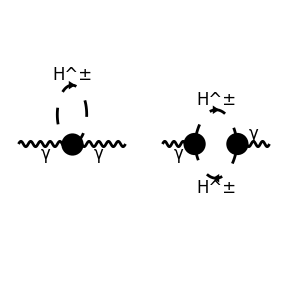

```mathematica
Paint[ΣγγDiag,ColumnsXRows->{2,1},Numbering->None];
```

```mathematica
ΣγγAmp[0]=DiracSimplify[FCFAConvert[CreateFeynAmp[ΣγγDiag,PreFactor->1,Truncated->True],IncomingMomenta->{k},OutgoingMomenta->{k},TransversePolarizationVectors->{k},Contract->True,LoopMomenta->{q},ChangeDimension->D,UndoChiralSplittings->True,List->False,DropSumOver->False,LorentzIndexNames->{µ,ν},FinalSubstitutions->{MH0->MH,MHch->MH}]/.FCGV[x_String]:>ToExpression[x],DiracSubstitute67->True]/.gc11->FCGV["EL"]//DiracSimplify//FCGVToSymbol;
```

```mathematica
(*Tensor decomposition into Passarino Veltman functions:*)
```

```mathematica
ΣγγAmp[1]= TID[ΣγγAmp[0],q,UsePaVeBasis->True,ToPaVe->True]//DiracSimplify;
```

```mathematica
Σγγ=(-I)/(2 Pi)^4PaVeLimitTo4[ΣγγAmp[1]];
```

```mathematica
(*Projecting out the transverse part*)
```

```mathematica
ΣγγT[0]=Contract[TransverseProjector*Σγγ];
```

```mathematica
%//FullSimplify//TraditionalForm
```

(EL^2 (2 ((k̄)^2+6 MH^2 B_0(0,MH^2,MH^2))+3 ((k̄)^2-4 MH^2) B_0((k̄)^2,MH^2,MH^2)))/(144 π^2)

#### Renormalization in MS bar scheme

```mathematica
ΣγγT[1]=ΣγγT[0]/.Pair[ Momentum[k], Momentum[k]]->kSquare;
```

```mathematica
ΣγγTHat[0]=FCHideEpsilon[PaXEvaluate[ΣγγT[1],PaXAnalytic->True]];
```

```mathematica
(* MS bar scheme *)
```

```mathematica
ΣγγTHat[1]=ΣγγTHat[0]-SMP["Delta"]*Coefficient[ΣγγTHat[0],SMP["Delta"]];
```

```mathematica
(* Derivative of  *)
```

```mathematica
DΣγγTHat[0]=D[ΣγγTHat[1],kSquare];
```

```mathematica
(*  at 0 *)
```

```mathematica
DΣγγTHatFor0=DΣγγTHat[0]//Series[#,{kSquare,0,0}]&//Normal;
```

```mathematica
%//FullSimplify//TraditionalForm
```

(EL^2 log(μ^2/(4 π^2 MH^2)))/(48 π^2)

### WW

```mathematica
ΣWWDiag=InsertFields[TopoΣ,{V[3]}->{V[3]},Model->{"tripletSM"},GenericModel->{"tripletSM"},InsertionLevel->{Particles},ExcludeParticles->{S[1],V[1|2|3|4],U[1|2|3|4|11|12|31|32],F[_,{_}]}];
```

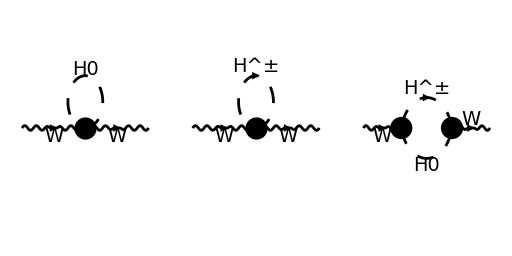

```mathematica
Paint[ΣWWDiag,ColumnsXRows->{3,1},Numbering->None,ImageSize->{512,256}];
```

```mathematica
ΣWWAmp[0]=DiracSimplify[FCFAConvert[CreateFeynAmp[ΣWWDiag,PreFactor->1,Truncated->True],IncomingMomenta->{k},OutgoingMomenta->{k},TransversePolarizationVectors->{k},Contract->True,LoopMomenta->{q},ChangeDimension->D,UndoChiralSplittings->True,List->False,DropSumOver->False,LorentzIndexNames->{µ,ν},FinalSubstitutions->{MH0->MH,MHch->MH}]/.FCGV[x_String]:>ToExpression[x],DiracSubstitute67->True]/.gc28->(FCGV["EL"])/FCGV["SW"]/.gc24->-((FCGV["EL"])/FCGV["SW"])//DiracSimplify//FCGVToSymbol;
```

```mathematica
(*Tensor decomposition into Passarino Veltman functions:*)
```

```mathematica
ΣWWAmp[1]= TID[ΣWWAmp[0],q,UsePaVeBasis->True,ToPaVe->True]//DiracSimplify;
```

```mathematica
ΣWW=(-I)/(2 Pi)^4PaVeLimitTo4[ΣWWAmp[1]];
```

```mathematica
ΣWWT[0]=Contract[TransverseProjector*ΣWW];
```

```mathematica
%//FullSimplify//TraditionalForm
```

(EL^2 (2 ((k̄)^2+6 MH^2 B_0(0,MH^2,MH^2))+3 ((k̄)^2-4 MH^2) B_0((k̄)^2,MH^2,MH^2)))/(144 π^2 SW^2)

#### Renormalization in MS bar scheme

```mathematica
ΣWWT[1]=ΣWWT[0]/.Pair[ Momentum[k], Momentum[k]]->kSquare;
```

```mathematica
ΣWWTHat[0]=FCHideEpsilon[PaXEvaluate[ΣWWT[1],PaXAnalytic->True]];
```

```mathematica
(* MS bar scheme *)
```

```mathematica
ΣWWTHat[1]=ΣWWTHat[0]-SMP["Delta"]*Coefficient[ΣWWTHat[0],SMP["Delta"]];
```

```mathematica
(*  at  *)
```

```mathematica
ΣWWTHatForMW2=ΣWWTHat[1]/.kSquare->MW^2;
```

```mathematica
%//FullSimplify//TraditionalForm
```

(EL^2 (3 MW^4 log(μ^2/(4 π^2 MH^2))+8 MW^2 (MW^2-3 MH^2)+3 (MW^2-4 MH^2) √(MW^4-4 MH^2 MW^2) log((√(MW^4-4 MH^2 MW^2)+2 MH^2-MW^2)/(2 MH^2))))/(144 π^2 MW^2 SW^2)

## Higgsstrahlung@NLO

## Cross section

## LO

#### Amplitude

```mathematica
topoLO=CreateTopologies[0,2->2];
diagLO=InsertFields[topoLO,{-F[2,{1}],F[2,{1}]}->{V[2],S[1]},Model->{"tripletSM"},GenericModel->{"tripletSM"},InsertionLevel->{Particles},ExcludeParticles->{S[1],S[2],V[3|4],U[1|2|3|4|11|12|31|32],F[_,{_}]}];
```

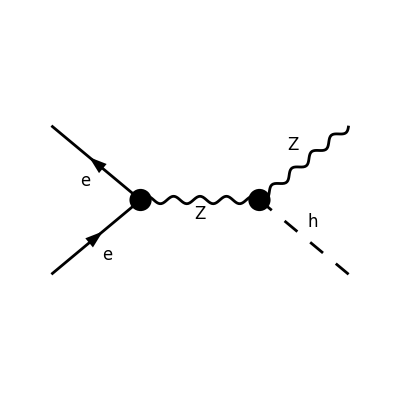

```mathematica
Paint[diagLO,ColumnsXRows->{2,1},Numbering->None];
```

```mathematica
FCClearScalarProducts[];
```

```mathematica
(*set the kinematics*)
```

```mathematica
SetMandelstam[s,t,u,p1,p2,-k1,-k2,0,0,MZ,mh];
```

```mathematica
(*define the matrix element*)
```

```mathematica
ampLO[0]=FCFAConvert[CreateFeynAmp[diagLO,PreFactor->1],IncomingMomenta->{p1,p2},OutgoingMomenta->{k1,k2},TransversePolarizationVectors->{k1},ChangeDimension->D,Contract->True,UndoChiralSplittings->True,List->False,DropSumOver->False,LorentzIndexNames->{µ,ν}]/.FCGV[x_String]:>ToExpression[x]//FCGVToSymbol//DiracSimplify[#,DiracSubstitute67->False]&;
```

```mathematica
(*matrix element squared*)
```

```mathematica
ampLOSquared[0]=ampLO[0]( ComplexConjugate[ampLO[0]])//FeynAmpDenominatorExplicit//FermionSpinSum[#,ExtraFactor->1/2^2]&//DiracSimplify//DoPolarizationSums[#,k1]&//FCReplaceD[#,D->4]&//TrickMandelstam[#,{s,t,u,MZ^2+mh^2}]& //DiracSimplify;
```

#### Matrix Element and cross section

```mathematica
(*LO matrix element squared*)
```

```mathematica
MLO2aux=ampLOSquared[0]/.gc44->(EL^2*(v)/(2*CW^2*SW^2))/.gc54L->(gv+ga) EL/.gc54R->(gv-ga) EL/.v->(2 SW CW MZ/EL)/.u->(MZ^2+mh^2-s-t)/.ME->0;
```

```mathematica
MLO2[t_]:=Evaluate[MLO2aux]
```

```mathematica
(*The differential cross section is given by dσLO/dt=(1/(16 Pi s^2))|M|^2 where M is the matrix element. We integrate over t and replace u from s+t+u=MZ^2+mh^2*)
```

```mathematica
σIntegrated=1/(16 Pi s^2)*Integrate[MLO2[t],t];
```

```mathematica
Clear[tLower]
```

```mathematica
(*Källén function*)
 κ[x_,y_,z_]:=√(x^2+y^2+z^2-2x y-2x z-2y z);
(*Kinematic limits for the integration in terms of κ=√λ, see definition of the Mandelstam variable t and take cosθ=±1*)
tUpper[s_]:=1/2 (MZ^2+mh^2-s+κ[s,MZ^2,mh^2]);
tLower[s_]:=1/2 (MZ^2+mh^2-s-κ[s,MZ^2,mh^2]);
```

```mathematica
(*LO cross section*)
σLOaux=(σIntegrated/.t->tUpper[s])- (σIntegrated/.t->tLower[s]);
```

```mathematica
(*Eq.(3.2) in the paper, typo in paper, missing square int he  κ inside the parenthesis*)
```

```mathematica
σLOliterature=(EL^4 (ga^2+gv^2) κ[s,MZ^2,mh^2] (12 MZ^2 s+κ[s,MZ^2,mh^2]^2))/(192 CW^2 π (MZ^2-s)^2 s^2 SW^2);
```

```mathematica
(*Validation*)
```

```mathematica
σLOaux==σLOliterature//TrickMandelstam[#,{s,t,u,MZ^2+mh^2}]&
```

True

## NLO

### Amplitude

```mathematica
LoopTopo=CreateTopologies[1,2->2,ExcludeTopologies->{WFCorrections,AllBoxes,SelfEnergies}];
```

```mathematica
LoopDiag=InsertFields[LoopTopo,{-F[2,{1}],F[2,{1}]}->{V[2],S[1]},Model->{"tripletSM"},GenericModel->{"tripletSM"},InsertionLevel->{Particles},ExcludeParticles->{S[1],S[2],V[3|4],U[1|2|3|4|11|12|31|32],F[_,{_}]}];
```

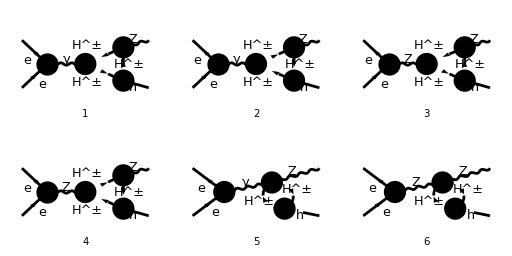

```mathematica
Paint[LoopDiag,ColumnsXRows->{3,2},Numbering->Simple,ImageSize->{512,256}];
```

```mathematica
ampsNLO[0]=FCFAConvert[CreateFeynAmp[LoopDiag,PreFactor->-I/(2Pi)^D],IncomingMomenta->{p1,p2},OutgoingMomenta->{k1,k2},LoopMomenta->{q},TransversePolarizationVectors->{k1},ChangeDimension->D,UndoChiralSplittings->True,List->True,DropSumOver->False,LorentzIndexNames->{µ,ν,µ1,ν1,µ2,ν2},FinalSubstitutions->{lam3->λ3,MH0->MH,MHch->MH}]/.gc11->FCGV["EL"]/.gc38->(FCGV["CW"]*FCGV["EL"])/FCGV["SW"]/.gc47->-FCGV["EL"]/.FCGV[x_String]:>ToExpression[x]//DiracSimplify[#,DiracSubstitute67->False]&//FCGVToSymbol;
```

```mathematica
(*Splitting the amplitudes into ZZ and γZ terms to simplify the analysis*)
```

```mathematica
ampsγZNLO[1]={ ampsNLO[0][[1]],ampsNLO[0][[2]],ampsNLO[0][[5]]};
```

```mathematica
ampsZZNLO[1]={ ampsNLO[0][[3]],ampsNLO[0][[4]],ampsNLO[0][[6]]};
```

```mathematica
(*Total of each contribution*)
```

```mathematica
ampsγZNLO[2] =Total[ampsγZNLO[1]];
```

```mathematica
ampsZZNLO[2] =Total[ampsZZNLO[1]];
```

```mathematica
(*The LO amplitude has an "I" prefactor:*)
```

```mathematica
AmpLO=ComplexConjugate[I ampLO[0]]//DiracSimplify;
```

### e + e - Z vertex contribution

#### Definitions

```mathematica
(*Looking at equation 3.8 the PaVe functions factorize so we do not have to look at all diagrams to reproduce the calculation:*)
```

```mathematica
AmpNLOZZ=TID[ampsZZNLO[2],q,UsePaVeBasis->True,ToPaVe->True]//DiracSimplify;
```

```mathematica
(*The following command allow us to use the Breitenlohner-Maison-’t Hooft-Veltman scheme when dealing with matrices in D dimensions, in particular to handle gamma5*)
```

```mathematica
FCSetDiracGammaScheme["BMHV"];
```

```mathematica
(*Product aiming to get Eq. 3.8, factor of two from 2 times real part*)
```

```mathematica
ampsquaredZZ=2AmpNLOZZ AmpLO/.gc54L->(gv+ga) EL/.gc54R->(gv-ga) EL/.gc44->(FCGV["EL"]^2*v)/(2*FCGV["CW"]^2*FCGV["SW"]^2)//FCGVToSymbol/.ME->0//FeynAmpDenominatorExplicit//FermionSpinSum[#,ExtraFactor->1/2^2]& //DoPolarizationSums[#,k1]&//FCReplaceD[#,D->4-2Epsilon]&//Series[#,{Epsilon,0,0}]&//Normal//ChangeDimension[#,4]&//DiracSimplify;
```

```mathematica
(*The following Eps[Momentum[k1],Momentum[k2],Momentum[p1],Momentum[p2]]->0 gets rid of the imaginary part of the product, this is a hack for this particular case*)
```

```mathematica
TwoReampZZ=ampsquaredZZ/.Eps[Momentum[k1],Momentum[k2],Momentum[p1],Momentum[p2]]->0/.ME^2->0//TrickMandelstam[#,{s,t,u,MZ^2+mh^2}]&;
```

```mathematica
(*The resultant expression is given in terms of tensor PaVe functions*)
```

```mathematica
TwoReampZZ//FullSimplify//TraditionalForm
```

1/(16 π^2 MZ^2 SW^4 (MZ^2-s)^2)EL^6 λ3 v^2 (ga^2+gv^2) ((mh^2 MZ^2+2 MZ^4-2 MZ^2 (t+u)+t u) B_0(mh^2,MH^2,MH^2)-2 (2 (mh^2 MZ^2+2 MZ^4-2 MZ^2 (t+u)+t u) C_00(mh^2,MZ^2,s,MH^2,MH^2,MH^2)+(2 MZ^2-t-u) (mh^2 MZ^2-t u) C_1(mh^2,s,MZ^2,MH^2,MH^2,MH^2)+(2 MZ^2-t-u) (mh^2 MZ^2-t u) (C_11(mh^2,s,MZ^2,MH^2,MH^2,MH^2)+C_12(mh^2,s,MZ^2,MH^2,MH^2,MH^2))))

```mathematica
(*We can look at the PaVe part alone*)
```

```mathematica
PavepartZZaux=(1/(16 MZ^2  π^2 SW^4(MZ^2-s)^2) EL^6 λ3 v^2(ga^2+gv^2)   )^-1 TwoReampZZ;
```

```mathematica
(*Writing down the Pavepart in terms of scalars PaVe functions A0,B0,C0 with the //PaVeReduce command:*)
```

```mathematica
PavepartZZaux=PavepartZZaux/.u->MZ^2+mh^2-s-t//PaVeReduce;
```

```mathematica
(*The PaVeLimitTo4 command is not defined for rational functions of D, so we multiply by (2-D) and then divide by it again*)
(* TODO: need to handle this in general *)
```

```mathematica
PavepartZZ4Daux=(2-D)PaVeLimitTo4[PavepartZZaux]//Contract;
```

```mathematica
(*and replace D->4. This is our final expression for the prodcut of matrix elements of the NLO calculation*)
```

```mathematica
PavepartZZ=PavepartZZ4Daux/(2-D)/.D->4;
```

#### Literature expression from Eq . (3.8) and C .8 in the paper

```mathematica
(*Let's do the general case*)
```

```mathematica
C22s=(1/(2*(Mh^4+(Mz^2-s)^2-2*Mh^2*(Mz^2+s))^2))*(2*Mz^2*(Mh^4+(Mz^2-s)^2-2*Mh^2*(Mz^2+s))-6*Mz^2*(Mz^2*(Mh^2-Mz^2+s)+(M1^2-M2^2)*(Mh^2+Mz^2-s))*PaVe[0,{MZ^2},{MH^2,MH^2}]-(Mh^6+(Mz^2-s)^2*(3*Mz^2-s)-Mh^4*(5*Mz^2+3*s)+Mh^2*(Mz^4+3*s^2)-2*(M1^2-M2^2)*(Mh^4+Mh^2*(4*Mz^2-s)+(Mz^2-s)^2))*PaVe[0,{mh^2},{MH^2,MH^2}]+((Mh^2-3*Mz^2)*(Mh^2-Mz^2)^2-(3*Mh^4+Mz^4)*s+(3*Mh^2+5*Mz^2)*s^2-s^3+(1/s)*(M1^2-M2^2)*((Mh^2-Mz^2)^3-5*(Mh^4-Mz^4)*s+(7*Mh^2-Mz^2)*s^2-3*s^3))*PaVe[0,{s},{MH^2,MH^2}]+2*(Mz^4*(Mh^4-2*Mh^2*(Mz^2-2*s)+(Mz^2-s)^2(*this square is missing in the paper*))+(M1^4+M2^4)*(Mh^4+2*Mh^2*(2*Mz^2-s)+(Mz^2-s)^2)-2*Mz^2*(Mh^4*(-2*M1^2+M2^2)+(Mz^2-s)^2*(M1^2-2*M2^2)+Mh^2*(Mz^2+s)*(M1^2+M2^2))-2*M1^2*M2^2*(Mh^4+2*Mh^2*(2*Mz^2-s)+(Mz^2-s)^2))*PaVe[0,{mh^2,MZ^2,s},{MH^2,MH^2,MH^2}]);
```

```mathematica
C23s=(1/(2*(Mh^4+(Mz^2-s)^2-2*Mh^2*(Mz^2+s))^2))*((Mh^2+Mz^2-s)*(Mh^4+(Mz^2-s)^2-2*Mh^2*(Mz^2+s))+(Mz^2*(-Mh^4+5*(Mz^2-s)^2-4*Mh^2*(Mz^2+s))-(M1^2-M2^2)*(Mh^4+(Mz^2-s)^2+2*Mh^2*(5*Mz^2-s)))*PaVe[0,{MZ^2},{MH^2,MH^2}]-((Mh^6+2*(Mz^2-s)^3-2*Mh^4*(3*Mz^2+2*s)+Mh^2*(3*Mz^4-8*Mz^2*s+5*s^2))-6*(M1^2-M2^2)*Mh^2*(Mh^2+Mz^2-s))*PaVe[0,{mh^2},{MH^2,MH^2}]+((Mh^6-(Mz^2-s)^2*(3*Mz^2+2*s)-Mh^4*(5*Mz^2+4*s)+Mh^2*(7*Mz^4-4*Mz^2*s+5*s^2))+(M1^2-M2^2)*((Mh^2-Mz^2)^2+2*(-3*Mh^4+Mh^2*Mz^2+2*Mz^4)*s+(3*Mh^2-5*Mz^2)*s^2+2*s^3))*PaVe[0,{s},{MH^2,MH^2}]+2*((Mz^2*((Mz^2-s)^3+Mh^4*(Mz^2+2*s)-Mh^2*(2*Mz^4-3*Mz^2*s+(*there is a wrong extra factor of 2 here in the paper*)s^2)))+3*(M1^4+M2^4)*Mh^2*(Mh^2+Mz^2-s)+M1^2*(Mh^2-Mz^2+s)*(Mh^4+2*Mh^2*(2*Mz^2-s)+(Mz^2-s)^2)+2*M2^2*((Mz^2-s)^3-Mh^4*(2*Mz^2+s)+Mh^2*(Mz^4-3*Mz^2*s+2*s^2))-6*M1^2*M2^2*Mh^2*(Mh^2+Mz^2-s))*PaVe[0,{mh^2,MZ^2,s},{MH^2,MH^2,MH^2}]);
```

```mathematica
C24s=(1/(4*(Mh^4+(Mz^2-s)^2-2*Mh^2*(Mz^2+s))))*((Mh^4+(Mz^2-s)^2-2*Mh^2*(Mz^2+s))-(Mz^2*(Mh^2-Mz^2+s)+(M1^2-M2^2)*(Mh^2+Mz^2-s))*PaVe[0,{MZ^2},{MH^2,MH^2}]+Mh^2*(Mh^2-Mz^2-s+2*M1^2-2*M2^2)*PaVe[0,{mh^2},{MH^2,MH^2}]+(s*(-Mh^2-Mz^2+s)-(M1^2-M2^2)*(Mh^2-Mz^2+s))*PaVe[0,{s},{MH^2,MH^2}]+(2*(Mh^2*Mz^2*s+(M1^4+M2^4)*Mh^2+M1^2*Mh^2*(Mh^2-Mz^2-s)+M2^2*((Mz^2-s)^2-Mh^2*(Mz^2+s))-2*M1^2*M2^2*Mh^2))*PaVe[0,{mh^2,MZ^2,s},{MH^2,MH^2,MH^2}]);
```

#### Validation with the literature

```mathematica
(*Part from eq 3.8 with only PaVe functions*)
```

```mathematica
Pavepartliterature=-2((t u +2s MZ^2 -mh^2MZ^2)(2C24s-1/2 PaVe[0,{mh^2},{MH^2,MH^2}])+(s+MZ^2-mh^2)(mh^2MZ^2-t u)(C22s-C23s))/.Mz->MZ/.Mh->mh/.M1->MH/.M2->MH;
```

```mathematica
(*B0(s) matching *)
```

```mathematica
Coefficient[Pavepartliterature, PaVe[0,{s},{MH^2,MH^2}]]==Coefficient[PavepartZZ, PaVe[0,{s},{MH^2,MH^2}]]//TrickMandelstam[#,{s,t,u,MZ^2+mh^2}]&//Simplify
```

True

```mathematica
(*B0(k2) matching*)
```

```mathematica
Coefficient[Pavepartliterature, PaVe[0,{mh^2},{MH^2,MH^2}]]==Coefficient[PavepartZZ, PaVe[0,{mh^2},{MH^2,MH^2}]]//TrickMandelstam[#,{s,t,u,MZ^2+mh^2}]&
```

True

```mathematica
(*B0(k1) matching*)
```

```mathematica
Coefficient[Pavepartliterature, PaVe[0,{MZ^2},{MH^2,MH^2}]]==Coefficient[PavepartZZ, PaVe[0,{MZ^2},{MH^2,MH^2}]]//TrickMandelstam[#,{s,t,u,MZ^2+mh^2}]&
```

True

```mathematica
(*C0(k1,k2) matching *)
```

```mathematica
Coefficient[Pavepartliterature,PaVe[0,{mh^2,MZ^2,s},{MH^2,MH^2,MH^2}]]==Coefficient[PavepartZZ,PaVe[0,{mh^2,MZ^2,s},{MH^2,MH^2,MH^2}]]//TrickMandelstam[#,{s,t,u,MZ^2+mh^2}]&
```

True

```mathematica
(*Independent term from the literature*)
```

```mathematica
Indtermliterature= Pavepartliterature-(Coefficient[Pavepartliterature, PaVe[0,{s},{MH^2,MH^2}]]* PaVe[0,{s},{MH^2,MH^2}]+Coefficient[Pavepartliterature, PaVe[0,{MZ^2},{MH^2,MH^2}]]* PaVe[0,{MZ^2},{MH^2,MH^2}]+Coefficient[Pavepartliterature, PaVe[0,{mh^2},{MH^2,MH^2}]]* PaVe[0,{mh^2},{MH^2,MH^2}]+Coefficient[Pavepartliterature,PaVe[0,{mh^2,MZ^2,s},{MH^2,MH^2,MH^2}]]*PaVe[0,{mh^2,MZ^2,s},{MH^2,MH^2,MH^2}]);
```

```mathematica
(*Independent term from the code*)
```

```mathematica
Indterm= PavepartZZ-(Coefficient[PavepartZZ,PaVe[0,{s},{MH^2,MH^2}]]* PaVe[0,{s},{MH^2,MH^2}]+Coefficient[PavepartZZ,PaVe[0,{MZ^2},{MH^2,MH^2}]]* PaVe[0,{MZ^2},{MH^2,MH^2}]+Coefficient[PavepartZZ,PaVe[0,{mh^2},{MH^2,MH^2}]]* PaVe[0,{mh^2},{MH^2,MH^2}]+Coefficient[PavepartZZ,PaVe[0,{mh^2,MZ^2,s},{MH^2,MH^2,MH^2}]]*PaVe[0,{mh^2,MZ^2,s},{MH^2,MH^2,MH^2}]);
```

```mathematica
(*Independent term matching *)
```

```mathematica
Indtermliterature==Indterm//TrickMandelstam[#,{s,t,u,MZ^2+mh^2}]&
```

True

### e + e - γ vertex contribution

```mathematica
AmpNLOγZ=TID[ampsγZNLO[2],q,UsePaVeBasis->True,ToPaVe->True]//DiracSimplify;
```

```mathematica
(*Product aiming to get Eq. 3.8, factor of two from 2 times real part*)
```

```mathematica
ampsquaredγZ=2AmpNLOγZ AmpLO/.gc54L->(gv+ga) EL/.gc54R->(gv-ga) EL/.gc44->(FCGV["EL"]^2*v)/(2*FCGV["CW"]^2*FCGV["SW"]^2)//FCGVToSymbol/.ME->0//FeynAmpDenominatorExplicit//FermionSpinSum[#,ExtraFactor->1/2^2]& //DoPolarizationSums[#,k1]&//FCReplaceD[#,D->4-2Epsilon]&//Series[#,{Epsilon,0,0}]&//Normal//ChangeDimension[#,4]&//DiracSimplify;
```

```mathematica
(*The following Eps[Momentum[k1],Momentum[k2],Momentum[p1],Momentum[p2]]->0 gets rid of the imaginary part of the product, this is a hack for this particular case*)
```

```mathematica
TwoReampγZ=ampsquaredγZ/.Eps[Momentum[k1],Momentum[k2],Momentum[p1],Momentum[p2]]->0/.ME^2->0//TrickMandelstam[#,{s,t,u,MZ^2+mh^2}]&;
```

```mathematica
(*The resultant expression is given in terms of tensor PaVe functions, this validates the earlier identification in the paper of the PaVe part of the expression factorizing from both contributions*)
```

```mathematica
TwoReampγZ//FullSimplify//TraditionalForm
```

1/(16 π^2 CW MZ^2 s SW^3 (MZ^2-s))EL^6 gv λ3 v^2 ((mh^2 MZ^2+2 MZ^4-2 MZ^2 (t+u)+t u) B_0(mh^2,MH^2,MH^2)-2 (2 (mh^2 MZ^2+2 MZ^4-2 MZ^2 (t+u)+t u) C_00(mh^2,MZ^2,s,MH^2,MH^2,MH^2)+(2 MZ^2-t-u) (mh^2 MZ^2-t u) C_1(mh^2,s,MZ^2,MH^2,MH^2,MH^2)+(2 MZ^2-t-u) (mh^2 MZ^2-t u) (C_11(mh^2,s,MZ^2,MH^2,MH^2,MH^2)+C_12(mh^2,s,MZ^2,MH^2,MH^2,MH^2))))

### Renormalized propagator

```mathematica
MWHat2=MW^2+Re[ΣWWTHatForMW2];
MZHat2=MZ^2+Re[ΣZZTHatForMZ2];
cHat=√(MWHat2/MZHat2);
sHat=√(1-cHat^2);
ELHat=EL(1-1/2 δZγγHat-1/2 sHat/cHat δZZγHat);
IWe3=-1/2;
Qe=-1;
gveff=(IWe3-2κHat sHat^2 Qe)/(2 sHat cHat);
gaeff=IWe3/(2 sHat cHat);
κHat=1-cHat/sHat ΣγZTHatFors/s;
ΓZMZ=Im[ΣHHatFors];
δZZZHat=-Re[DΣZZTHatforMZ2];
δZhHat=-Re[DΣHHatFormh2];
δZγγHat=-Re[DΣγγTHatFor0];
δZZγHat=2 ΣγZTHatFor0/MZ^2;
```

```mathematica
ρHat=1/(s-MZ^2+I ΓZMZ)(1+(Re[ΣZZTHatForMZ2]-Re[ΣZZTHatFors])/(s-MZ^2)+1/2 δZZZHat-1/2 Re[DΣHHatFormh2])/.v->(2 SW CW MZ/EL);
```

### Matrix Elements and cross section

```mathematica
(*NLO matrix element squared from self energies, typo in paper esq 3.1 and 3.7, missing factor of 1/2*)
```

```mathematica
Mself2=(Norm[ELHat]^4MZHat2(Norm[gveff]^2+Norm[gaeff]^2))/(2MZ^2Norm[sHat]^2 Norm[cHat]^2)(t u+2s MZ^2-mh^2MZ^2)Norm[ρHat]^2/.ScaleMu->μ/.u->(MZ^2+mh^2-s-t);
```

```mathematica
MTree2=N[Mself2];
```

```mathematica
(*NLO matrix element squared from intereference term with vertex contribution*)
```

```mathematica
MvertexMtree=Re[ComplexExpand[N[PaXEvaluate[(TwoReampZZ+TwoReampγZ)/.v->(2 SW CW MZ/EL)/.u->(MZ^2+mh^2-s-t) ,PaXC0Expand->True]]]];
```

```mathematica
(*The differential cross section is given by dσNLO/dt=(1/(16 Pi s^2))|Mtot,corr|^2 with Mtot,corr given by Eq.3.6*)
```

```mathematica
Mtotcorr2[λ3_,MH_,μ_,s_,t_]:=Evaluate[(MTree2+MvertexMtree)-MLO2aux]
```

```mathematica
σ1loop[λ3_,MH_,μ_,s_]:=(1/(16 Pi s^2)*NIntegrate[Mtotcorr2[λ3,MH,μ,s,tp],{tp,tLower[s],tUpper[s]}])
```

### Constants from PDG 2025

```mathematica
mh=Rationalize[125.2];
MZ=Rationalize[91.1880];
MW=Rationalize[80.3692];
CW=Rationalize[MW/MZ];
SW=√(1-CW^2);
α=Rationalize[1/137.036];
EL=√(4Pi α);
gv=Rationalize[(-1/2+2SW^2)/(2CW*SW)];
ga=Rationalize[(-1/(4CW*SW))];
ΓZ=Rationalize[2.4952];
convfactor=0.3894*10^12;(*from GeV^-2 to fb*)
```

## Plots

```mathematica
σLO[s_]:= Evaluate[σLOaux]
```

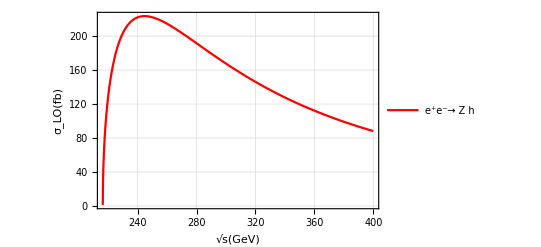

```mathematica
Plot[convfactor σLO[s^2],{s,200,400},PlotStyle->{Red},Frame->True,GridLines->Automatic,FrameLabel->{Style["√s(GeV)",FontSize->18,FontFamily->"Times"],Style["σ_LO(fb)",FontSize->18,FontFamily->"Times"]},PlotRange->All,PlotLegends->Placed[{Style["e^+e^-→ Z h",FontFamily->"Times",FontSize->12]},{Right,Top}]]
```

```mathematica
Manipulate[Abs[σ1loop[λ3,MH,μ,s]/σLO[s]],{s,240,400},{MH,200,700},{λ3,-5,5},{μ,MZ,10^4}]
```

```mathematica
(*ContourPlot takes around 35 minutes to evaluate this plot on a MacBook Pro 2.2 GHz 6-Core Intel Core i7*)
```

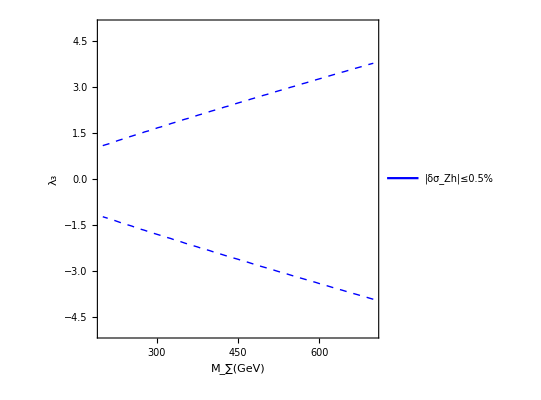

```mathematica
ContourPlot[Abs[σ1loop[λ3,MH,MZ,240]]/σLO[240],{MH,200,700},{λ3,-5,5},Contours->{0.5/100},ContourStyle->{{Blue,Dashed}},ContourShading->None,FrameTicksStyle->Directive[Bold,12],FrameLabel->{Style["M_∑(GeV)",FontSize->18,FontFamily->"Times",Bold],Style["λ_3",FontSize->18,FontFamily->"Times",Bold]},PlotLegends->Placed[{Style["|δσ_Zh|≤0.5%",FontFamily->"Times",FontSize->12]},{Left,Bottom}]]
```

```mathematica
(*RegionPlot has a bug that does not allow NIntegrate to be evaluated properly, I already tried some solutions on stackexchange but none worked out, https://mathematica.stackexchange.com/questions/94402/error-with-nintegrate-and-regionplot*)
```

```mathematica
(*I have not tried the Plot3D option here though, https://mathematica.stackexchange.com/questions/189717/regionplot-evaluating-nintegrate-before-assigning-variable-values-and-resulting*)
```

```mathematica
(*RegionPlot[ImplicitRegion[(Abs[σ1loop[λ3,MH,MZ,240]]/σLO[240])≤0.005,{{MH,200,700},{λ3,-5,5}}],BoundaryStyle->{Black},PlotRange->{{200,700},{-5,5}},Frame->True,FrameTicksStyle->Directive[Bold,12],FrameLabel->{Style["M_∑(GeV)",FontSize->18,FontFamily->"Times",Bold],Style["λ_3",FontSize->18,FontFamily->"Times",Bold]},PlotStyle->Directive[Opacity[0.5,Cyan]],PlotLegends->Placed[{Style["|δσ_Zh|≤0.5%",FontFamily->"Times",FontSize->12]},{Left,Bottom}]]*)
```